# KOMPLEKSNA ŠTEVILA ( ℂ )

## Oznake in sestava: ℂ ; a, b ∈ ℝ)

z           =       a    +    b ⅈ

a           =       Realna komponenta;                              Re[z]

b         =       Imaginarna komponenta (brez i);      Im[z]

ⅈ            =       Imaginarna enota;                                  (Esc)ii(Esc)

z̄           =       Konjugirana vrednost;                          Conjugate[z]; (Esc)co(Esc)

|z|    =      Absolutna  vrednost;                              Abs[z]

Arg[z] =      Argument kota;                                       Arg[z];

|z|=  √(a^2+b^2)

|z_1+z_2|=|z_1|+|z_2|

arg(z_1, z_2)=arg(z_1)+arg(z_2)

arg (z_1/z_2)=arg(z_1)-arg(z_2)

√-a =  ⅈ √a ;  (a > 0)

Še nekaj bližnjic, ki sem jih uporabljal pri sestavi seminarske naloge:

ⅈ        ⟶ (Esc)ii(Esc)

z_1     ⟶ (Shift+ _)

z^2     ⟶ (Shift+ 6)

γ      ⟶ (Esc)gamma(Esc)

θ      ⟶ (Esc)th(Esc)

□/□      ⟶ (Shift+Control+7)

√□ ⟶ (Shift+2)

## ⅈ → Odpravimo eksponent

```mathematica
i^0  =     1
i^1  =     i
i^2  =  -1
i^3  =  -i
i^4  =     1
PRIMER: 
i^715 = i^3 = -i
->razbijemo potenco ; 715 = 15 : 4 = 3  ( 3 je novi eksponent)
```

```mathematica
ⅈ^715
```

-ⅈ

## z̄ → Konjugiranje: - Conjugate[z]; - “(Esc)co(Esc)”

Pri konjugiranju se spremeni predznak pred imaginarno komponento:

z  =  a + b i 
z̄ = a - b i

Računanje z Z̄ :

OverBar[Z+W] = Z̄+ W̄

OverBar[Z-W] = Z̄- W̄

OverBar[Z*W] = Z̄* W̄

|Z̄| = |Z|

OverBar[Z̄]  =  Z

Z^-1 = (z̄)/(|z|^2)

### Nekaj primerov:

OverBar[( 2+i )] =  2-i

```mathematica
Conjugate[2+ⅈ]
```

2-ⅈ

( ī )^3    =  ( -i )^3  =  -i^3 = -(-i )  =  i

```mathematica
Conjugate[(ⅈ)^3]
```

ⅈ

( OverBar[7] )^2   =  7^2  =  49

```mathematica
Conjugate[7^2]
```

49

OverBar[( 2+i )( 3-4 i )] = (2-i )(3+4 i )=6+8 i -3 i-4 i^2=6+5 i +4 = 10+5 i

```mathematica
Conjugate[(2+ⅈ)(3-4ⅈ)]
```

10+5 ⅈ

OverBar[( 2+i )^2]= ( 2-i )^2 = 4-4i-1 = 3 - 4 i

```mathematica
Conjugate[(2+ⅈ)^2]
```

3-4 ⅈ

( OverBar[(2 + i)/(3 - i)] ) = (2 - i)/(3 + i)*(3 - i)/(3 - i)= (5 - 5 i)/(9 + 1)= (5 ( 1 - i ))/10= 1/2- 1/2 i

```mathematica
Conjugate[2+ⅈ]/Conjugate[3-ⅈ]
```

1/2-ⅈ/2

## | Z | → Absolutna vrednost: - Abs[Z]

Absolutna vrednost predstavlja dolžino krajevnega vektorja. Pravimo, da sta dve števili enaki, ko imata enako absolutno vrednost.

Lastnosti absolutne vrednosti:

|z · w|= |z| · |w|

|Z/W|= (|Z|)/(|W|)

|z - w| = razdalja med točkama z in w

|z| = r ;   radij krožnice

|z| =  √(a^2 + b^2)

Primer: |z-w| = |-2-ⅈ-(5-ⅈ)|=|-2-ⅈ-5+ⅈ| = 7

```mathematica
z = -2-ⅈ;
w= 5-ⅈ;
```

```mathematica
Abs[z-w]
```

7

Primer: z= -2-ⅈ      ⟶     |z|=√((-2)^2+(-1)^2)=√(4+2)=√5

```mathematica
z= -2-ⅈ
-2-ⅈ
```

```mathematica
Abs[z]
```

√5

## Polarni zapis kompleksnega “CX”števila:

z=x+ⅈ y  ⟶  x=r cosθ,   y=r sinθ       ⟹     r(cosθ+ⅈ sinθ)

z=|z|(cosθ+ⅈ sinθ)

|z|= r

z_1·z_2=r(cos(θ_1+θ_2)+ⅈ sin(θ_1+θ_2)

z_1/z_2=(z_(1·)OverBar[z_2])/(|z_2|^2)=r_1/r_2=(cos(θ_1-θ_2)+ⅈ sin(θ_1-θ_2)

z̄=r(cos(-θ)+ⅈ sin(-θ)

γ=arctan(x/y)

Primer 1:

```mathematica
graf1 = 1
graf2 = 1 + 1/10 Sin[10 s]
```

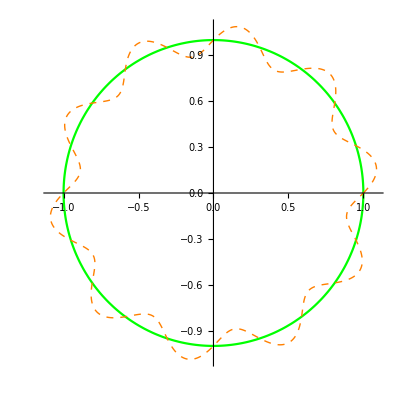

```mathematica
PolarPlot[{graf1, graf2}, {s, 0, 2Pi},PlotStyle->{Green, Directive[Dashed, Thick, Orange]}]
```

Primer 2:

```mathematica
θ=Pi/6
```

π/6

30.

```mathematica
r=4;
```

```mathematica
x=r·Cos(0);
```

```mathematica
y=r·Sin(θ);
```

```mathematica
P=x+ⅈ·y;
```

```mathematica
ComplexVector[r,θ]:=Arrow[{{0,0},{r*Cos[θ],r*Sin[θ]}}]
```

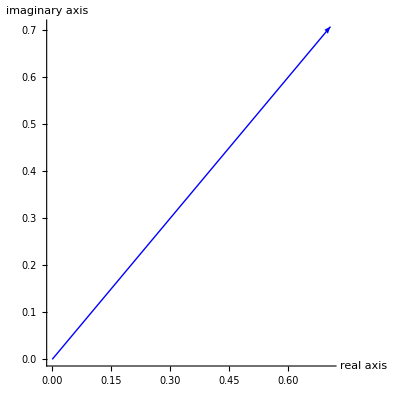

```mathematica
Graphics[{Blue,ComplexVector[1,Pi/4]},Axes->True,AxesLabel->{"real axis","imaginary axis"}]
```

Primer 3:

#### Določi točke na enotski krožnici:

#### z^4= -8 + 8 √3 ⅈ

```mathematica
z=-8+I 8Sqrt[3];
```

Prva tocka:

```mathematica
ϕ0 =Arg[z] /4 + (0Pi)/2
```

π/6

```mathematica
N[ϕ0/°]
```

30.

Druga tocka:

```mathematica
ϕ1 =Arg[z] /4 + (1Pi)/2
```

(2 π)/3
120.

Tretja tocka:

```mathematica
ϕ2 =Arg[z] /4 + (2Pi)/2
```

(7 π)/6
210.

Cetrta tocka:

```mathematica
ϕ3=Arg[z] /4 + (3Pi)/2
```

(5 π)/3
300.

```mathematica
ClearAll[z]
```

```mathematica
eq=Solve[{z^4==-8+I 8Sqrt[3]},{z}]
```

{{z→-2^(3/4) (-1+ⅈ √3)^(1/4)},{z→-ⅈ 2^(3/4) (-1+ⅈ √3)^(1/4)},{z→ⅈ 2^(3/4) (-1+ⅈ √3)^(1/4)},{z→2^(3/4) (-1+ⅈ √3)^(1/4)}}

```mathematica
Graphics[Point[ReIm[z/.eq]]]
```

-Graphics-

```mathematica
Abs[z] Exp[I Arg[z]]
```

```mathematica
16 ⅇ^((2 ⅈ π)/3)
```

```mathematica
N[eq]
```

{{z→-1.73205-1. ⅈ},{z→1.-1.73205 ⅈ},{z→-1.+1.73205 ⅈ},{z→1.73205+1. ⅈ}}

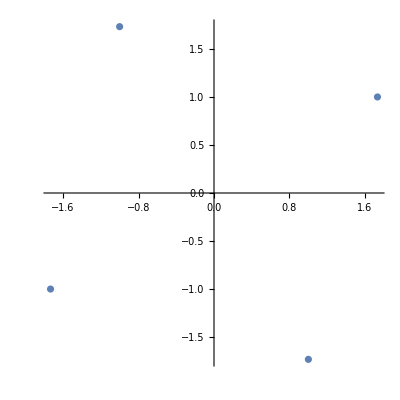

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{-1.7320508075688772-0.9999999999999999 ⅈ,0.9999999999999999-1.7320508075688772 ⅈ,-0.9999999999999999+1.7320508075688772 ⅈ,1.7320508075688772+0.9999999999999999 ⅈ},AspectRatio->1]
```

Še nekaj primerov:

a.)



```mathematica
ParametricPlot[ReIm[E^(I  ω)],{ω, 0, 2π}]
```

b.)

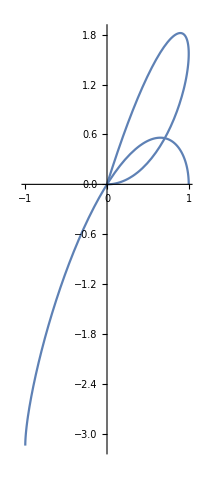

```mathematica
PolarPlot[AbsArg[E^(ⅈ ω)],{ω, 0, Pi}]
```

c.)

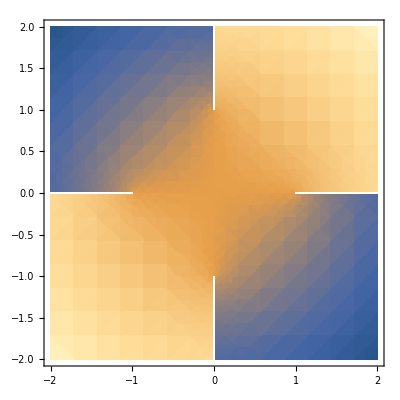

```mathematica
DensityPlot[Im[ArcSin[(x+I y)^2]],{x,-2,2},{y,-2,2}]
```

Razširi izraz kompleksnega števila:

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

Pretvori izraz med ekponentno in trigonomično obliko:

```mathematica
ExpToTrig[E^(I x)]
```

Cos[x]+ⅈ Sin[x]

```mathematica
TrigToExp[%]
```

ⅇ^(ⅈ x)

Vrne realni in imaginarni del v seznamu:

```mathematica
ReIm[-8+8Sqrt[3]ⅈ]
```

{-8,8 √3}

Poišči absolutno vrednost in argument:

```mathematica
AbsArg[(1+I)]
```

{√2,π/4}